## This notebook, calculates the frequency of a charged massles scalar field around a RN black hole considering a mirror: based on Phys Rev D 70 044039 (2004). Aveiro 20 feb 2013. check: mirrorFreq.mw

```mathematica
Exit
```

```mathematica
Clear; MaxExtraPrecision=100;
M=1;l=1; mu=0.1; qscal=0.9;
```

```mathematica
winit=(0.2-0.00005*I)
```

0.2-0.00005 ⅈ

```mathematica
(*Define the Function of w as the solution of the Diferential equation given a value of r1, the position of the mirror. The returning value is the solution evaluated at r1 *)
```

```mathematica
LeavP1[w_?NumberQ]:=
Module[{Res},
r0=M+10^(-3);r1=30 ;wc=qscal;
qsol=-Sqrt[mu*mu-w*w] ;
rhosol=-2*I*M*(w-wc);
sigmasol=M*(qscal*w+mu^2-2*w^2);
sol=NDSolve[{D[Rs[r],{r,2}]+2*D[Rs[r],{r,1}]/(r-M)+( (w*r^2-qscal*M*r)^2/(r-M)^4- 1/(r-M)^2*(mu^2*r^2+l*(l+1))  )*Rs[r]==0,Rs[r0]==M^(sigmasol-rhosol-1)*Exp[qsol*r0+I*M^2*(w-wc)/(r0-M)]*(r0-M)^(rhosol),Rs'[r0]==M^(sigmasol-rhosol-1)*Exp[qsol*r0+I*M^2*(w-wc)/(r0-M)]*(rhosol*(r0-M)-I*M^2*(w-wc))*(r0-M)^(rhosol-2)},Rs,{r,r0,r1},
          MaxSteps->50000];
Res=Rs[r1]/.sol];
```

```mathematica
(*Find the root of this function, this w is such as the value of the function is zero at *)
```

```mathematica
wres=FindRoot[LeavP1[w]==0,{w,winit}] [[1]][[2]]
```

0.218905+2.99568×10^-6 ⅈ

```mathematica
(*Check that the solution obtained is the solution wanted and plot it*)
```

```mathematica
r0=M+10^(-3);r1=30; wc=qscal;
qsol=-Sqrt[mu*mu-wres*wres] ;
rhosol=-2*I*M*(wres-wc);
sigmasol=M*(qscal*wres+mu^2-2*wres^2);
(*potsol= 1/f*(  w-qscal*Q/r )^2-l*(l+1)/r^2-mu^2;*)
sol=NDSolve[
{D[Rs[r],{r,2}]+2*D[Rs[r],{r,1}]/(r-M)+( (wres*r^2-qscal*M*r)^2/(r-M)^4 - 1/(r-M)^2*(mu^2*r^2+l*(l+1))  )*Rs[r]==0,Rs[r0]==M^(sigmasol-rhosol-1)*Exp[qsol*r0+I*M^2*(wres-wc)/(r0-M)]*(r0-M)^(rhosol),Rs'[r0]==M^(sigmasol-rhosol-1)*Exp[qsol*r0+I*M^2*(wres-wc)/(r0-M)]*(rhosol*(r0-M)-I*M^2*(wres-wc))*(r0-M)^(rhosol-2)},Rs,{r,r0,r1},
          MaxSteps->50000];
```

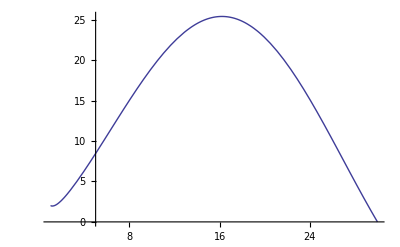

```mathematica
Plot[{2.01*Abs[Rs[r]/.sol]},{r,r0,r1}]
```

```mathematica
(*Now, do the previous procedure for several values of r1, the position of the mirror:
I approach the value from right and left because dont know the rate of change in the function,    in some cases is very high and then fails from one step to other.*)
```

```mathematica
winit=(0.2-0.00005*I);
ie=0;While[ie<101,NITMAX=250;
LeavP1[w_?NumberQ]:=
Module[{Res},
r0=M+5*10^(-4);r1=30 +ie/5;wc=qscal;
qsol=-Sqrt[mu*mu-w*w] ;
rhosol=-2*I*M*(w-wc);
sigmasol=M*(qscal*w+mu^2-2*w^2);

sol=NDSolve[{D[Rs[r],{r,2}]+2*D[Rs[r],{r,1}]/(r-M)+( (w*r^2-qscal*M*r)^2/(r-M)^4- 1/(r-M)^2*(mu^2*r^2+l*(l+1))  )*Rs[r]==0,Rs[r0]==M^(sigmasol-rhosol-1)*Exp[qsol*r0+I*M^2*(w-wc)/(r0-M)]*(r0-M)^(rhosol),Rs'[r0]==M^(sigmasol-rhosol-1)*Exp[qsol*r0+I*M^2*(w-wc)/(r0-M)]*(rhosol*(r0-M)-I*M^2*(w-wc))*(r0-M)^(rhosol-2)},Rs,{r,r0,r1},
          MaxSteps->50000];
Res=Rs[r1]/.sol];
wres=FindRoot[LeavP1[w]==0,{w,winit}] [[1]][[2]];
witer[ie]=wres;
radit[ie]=r1;
winit=wres-0.001;
ie=ie+1
]
t1r=Table[{N[radit[n],10],Re[witer[n]]},{n,0,100}];
t2r=Table[{N[radit[n],10],Im[witer[n]]},{n,0,100}];
```

```mathematica
(*Calculate the values leftward*)
```

```mathematica
winit=(0.2-0.00005*I);
ie=0;While[ie<51,NITMAX=250;
LeavP1[w_?NumberQ]:=
Module[{Res},
r0=M+5*10^(-4);r1=30 -ie/5;wc=qscal;
qsol=-Sqrt[mu*mu-w*w] ;
rhosol=-2*I*M*(w-wc);
sigmasol=M*(qscal*w+mu^2-2*w^2);
sol=NDSolve[{D[Rs[r],{r,2}]+2*D[Rs[r],{r,1}]/(r-M)+( (w*r^2-qscal*M*r)^2/(r-M)^4- 1/(r-M)^2*(mu^2*r^2+l*(l+1))  )*Rs[r]==0,Rs[r0]==M^(sigmasol-rhosol-1)*Exp[qsol*r0+I*M^2*(w-wc)/(r0-M)]*(r0-M)^(rhosol),Rs'[r0]==M^(sigmasol-rhosol-1)*Exp[qsol*r0+I*M^2*(w-wc)/(r0-M)]*(rhosol*(r0-M)-I*M^2*(w-wc))*(r0-M)^(rhosol-2)},Rs,{r,r0,r1},
          MaxSteps->50000];
Res=Rs[r1]/.sol];
wres=FindRoot[LeavP1[w]==0,{w,winit}] [[1]][[2]];
witer[ie]=wres;
radit[ie]=r1;
winit=wres+0.0008;
ie=ie+1

]
t1l=Table[{N[radit[n],10],Re[witer[n]]},{n,0,50}]
t2l=Table[{N[radit[n],10],Im[witer[n]]},{n,0,50}];
```

{{30.,0.218905},{29.8,0.219928},{29.6,0.220966},{29.4,0.222018},{29.2,0.223085},{29.,0.224168},{28.8,0.225266},{28.6,0.22638},{28.4,0.227511},{28.2,0.228657},{28.,0.229821},{27.8,0.231003},{27.6,0.232201},{27.4,0.233418},{27.2,0.234653},{27.,0.235907},{26.8,0.23718},{26.6,0.238473},{26.4,0.239786},{26.2,0.241119},{26.,0.242473},{25.8,0.243848},{25.6,0.245245},{25.4,0.246664},{25.2,0.248106},{25.,0.249571},{24.8,0.25106},{24.6,0.252574},{24.4,0.254112},{24.2,0.255676},{24.,0.257266},{23.8,0.258882},{23.6,0.260526},{23.4,0.262198},{23.2,0.263898},{23.,0.265628},{22.8,0.267388},{22.6,0.269178},{22.4,0.271},{22.2,0.272854},{22.,0.274741},{21.8,0.276662},{21.6,0.278618},{21.4,0.28061},{21.2,0.282638},{21.,0.284704},{20.8,0.286808},{20.6,0.288951},{20.4,0.291136},{20.2,0.293361},{20.,0.29563}}

```mathematica
winit=(0.3-0.00005*I);
ie=0;While[ie<25,NITMAX=250;
LeavP1[w_?NumberQ]:=
Module[{Res},
r0=M+5*10^(-4);r1=20 -ie/5;wc=qscal;
qsol=-Sqrt[mu*mu-w*w] ;
rhosol=-2*I*M*(w-wc);
sigmasol=M*(qscal*w+mu^2-2*w^2);
sol=NDSolve[{D[Rs[r],{r,2}]+2*D[Rs[r],{r,1}]/(r-M)+( (w*r^2-qscal*M*r)^2/(r-M)^4- 1/(r-M)^2*(mu^2*r^2+l*(l+1))  )*Rs[r]==0,Rs[r0]==M^(sigmasol-rhosol-1)*Exp[qsol*r0+I*M^2*(w-wc)/(r0-M)]*(r0-M)^(rhosol),Rs'[r0]==M^(sigmasol-rhosol-1)*Exp[qsol*r0+I*M^2*(w-wc)/(r0-M)]*(rhosol*(r0-M)-I*M^2*(w-wc))*(r0-M)^(rhosol-2)},Rs,{r,r0,r1},
          MaxSteps->50000];
Res=Rs[r1]/.sol];
wres=FindRoot[LeavP1[w]==0,{w,winit}] [[1]][[2]];
witer[ie]=wres;
radit[ie]=r1;
winit=wres+0.001;
ie=ie+1

]
t1l2=Table[{N[radit[n],10],Re[witer[n]]},{n,0,24}]
t2l2=Table[{N[radit[n],10],Im[witer[n]]},{n,0,24}];
```

{{20.,0.29563},{19.8,0.297942},{19.6,0.3003},{19.4,0.302704},{19.2,0.305155},{19.,0.307656},{18.8,0.310207},{18.6,0.31281},{18.4,0.315466},{18.2,0.318177},{18.,0.320944},{17.8,0.323769},{17.6,0.326655},{17.4,0.329602},{17.2,0.332612},{17.,0.335688},{16.8,0.338832},{16.6,0.342045},{16.4,0.34533},{16.2,0.348689},{16.,0.352124},{15.8,0.355638},{15.6,0.359234},{15.4,0.362914},{15.2,0.366681}}

```mathematica
winit=(0.35-0.00005*I);
ie=0;While[ie<26,NITMAX=250;
LeavP1[w_?NumberQ]:=
Module[{Res},
r0=M+5*10^(-4);r1=15 -ie/5;wc=qscal;
qsol=-Sqrt[mu*mu-w*w] ;
rhosol=-2*I*M*(w-wc);
sigmasol=M*(qscal*w+mu^2-2*w^2);
sol=NDSolve[{D[Rs[r],{r,2}]+2*D[Rs[r],{r,1}]/(r-M)+( (w*r^2-qscal*M*r)^2/(r-M)^4- 1/(r-M)^2*(mu^2*r^2+l*(l+1))  )*Rs[r]==0,Rs[r0]==M^(sigmasol-rhosol-1)*Exp[qsol*r0+I*M^2*(w-wc)/(r0-M)]*(r0-M)^(rhosol),Rs'[r0]==M^(sigmasol-rhosol-1)*Exp[qsol*r0+I*M^2*(w-wc)/(r0-M)]*(rhosol*(r0-M)-I*M^2*(w-wc))*(r0-M)^(rhosol-2)},Rs,{r,r0,r1},
          MaxSteps->50000];
Res=Rs[r1]/.sol];
wres=FindRoot[LeavP1[w]==0,{w,winit}] [[1]][[2]];
witer[ie]=wres;
radit[ie]=r1;
winit=wres+0.0008;
ie=ie+1

]
t1l3=Table[{N[radit[n],10],Re[witer[n]]},{n,0,25}]
t2l3=Table[{N[radit[n],10],Im[witer[n]]},{n,0,25}];
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

{{15.,0.370538},{14.8,0.374488},{14.6,0.378534},{14.4,0.38268},{14.2,0.386928},{14.,0.391284},{13.8,0.395749},{13.6,0.400329},{13.4,0.405028},{13.2,0.409849},{13.,0.414798},{12.8,0.419879},{12.6,0.425097},{12.4,0.430458},{12.2,0.435967},{12.,0.44163},{11.8,0.447453},{11.6,0.453441},{11.4,0.459603},{11.2,0.465944},{11.,0.472473},{10.8,0.479197},{10.6,0.486123},{10.4,0.493261},{10.2,0.50062},{10.,0.508208}}

```mathematica
winit=(0.5-0.00005*I);
ie=0;While[ie<26,NITMAX=250;
LeavP1[w_?NumberQ]:=
Module[{Res},
r0=M+5*10^(-4);r1=10 -ie/5;wc=qscal;
qsol=-Sqrt[mu*mu-w*w] ;
rhosol=-2*I*M*(w-wc);
sigmasol=M*(qscal*w+mu^2-2*w^2);
sol=NDSolve[{D[Rs[r],{r,2}]+2*D[Rs[r],{r,1}]/(r-M)+( (w*r^2-qscal*M*r)^2/(r-M)^4- 1/(r-M)^2*(mu^2*r^2+l*(l+1))  )*Rs[r]==0,Rs[r0]==M^(sigmasol-rhosol-1)*Exp[qsol*r0+I*M^2*(w-wc)/(r0-M)]*(r0-M)^(rhosol),Rs'[r0]==M^(sigmasol-rhosol-1)*Exp[qsol*r0+I*M^2*(w-wc)/(r0-M)]*(rhosol*(r0-M)-I*M^2*(w-wc))*(r0-M)^(rhosol-2)},Rs,{r,r0,r1},
          MaxSteps->50000];
Res=Rs[r1]/.sol];
wres=FindRoot[LeavP1[w]==0,{w,winit}] [[1]][[2]];
witer[ie]=wres;
radit[ie]=r1;
winit=wres+0.0008;
ie=ie+1

]
t1l4=Table[{N[radit[n],10],Re[witer[n]]},{n,0,25}];
t2l4=Table[{N[radit[n],10],Im[witer[n]]},{n,0,25}]
```

{{10.,0.0000237161},{9.8,0.000023927},{9.6,0.0000241081},{9.4,0.0000243032},{9.2,0.0000243623},{9.,0.0000244712},{8.8,0.0000244964},{8.6,0.0000244491},{8.4,0.0000242966},{8.2,0.0000241746},{8.,0.0000238755},{7.8,0.0000235326},{7.6,0.0000231404},{7.4,0.0000225872},{7.2,0.000021981},{7.,0.0000212133},{6.8,0.0000202726},{6.6,0.0000192654},{6.4,0.0000180581},{6.2,0.000016769},{6.,0.000015235},{5.8,0.0000136602},{5.6,0.0000118891},{5.4,0.0000100584},{5.2,8.10582×10^-6},{5.,6.17671×10^-6}}

```mathematica
(*The imaginary part vs the radius*)
```

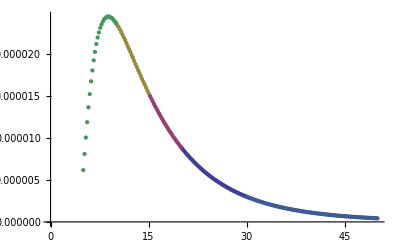

```mathematica
ListPlot[{t2l,t2l2,t2l3,t2l4,t2r},Axes->True]
```

```mathematica
(*Real vs Radius*)
```

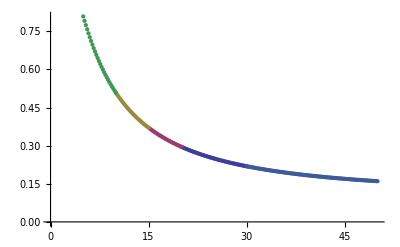

```mathematica
ListPlot[{t1l,t1l2,t1l3,t1l4,t1r}]
```

```mathematica
Export["/home/h/skoli/pt/rnef/mathematica/mirror-radius/mu0.1/Q=1.0/q=0.9/R.dat",Join[t1l,t1l2,t1l3,t1l4,t1r]]
Export["/home/h/skoli/pt/rnef/mathematica/mirror-radius/mu0.1/Q=1.0/q=0.9/I.dat",Join[t2l,t2l2,t2l3,t2l4,t2r]]
```

/home/h/skoli/pt/rnef/mathematica/mirror-radius/mu0.1/Q=1.0/q=0.9/R.dat

/home/h/skoli/pt/rnef/mathematica/mirror-radius/mu0.1/Q=1.0/q=0.9/I.dat

```mathematica
(*This is for estimate the "Analytical" value using Cardoso's bomb *)
```

```mathematica
(*Radius*)
```

```mathematica
rp=M+Sqrt[M^2-M^2]
rm=M-Sqrt[M^2-M^2]
rmirror=40
```

1

1

40

```mathematica
(*Frequencies*)
```

```mathematica
wc=qscal*M/rp
wtilde=(wa-wc)*(rp^2/(rp-rm))
```

0.3

Power::infy: Infinite expression 1/0 encountered.

ComplexInfinity

```mathematica
(*Nodes*)
```

```mathematica
n=0
```

0

```mathematica
(*First aproximation, the root of the Bessel function (has to be the n+1 root, otherwise the 1st is zero!)*)
```

```mathematica
jl12n=N[BesselJZero[l+1/2,n+1],10]
```

4.493409459

```mathematica
wfa=jl12n/rmirror
```

0.1123352365

```mathematica
(*Let's calculate the imaginary part, delta, we need some definitions in advance*)
```

```mathematica
Product[i^2+4*wtilde^2,{i,1,l}]
```

1+18.2044 (-0.45+wa)^2

```mathematica
gamm=(Factorial[l]/Factorial2[(2*l-1)])^2*rp^2*(rp-rm)^(2*l)/Factorial[2*l]/Factorial[2*l+1]*2/(2*l+1)*Product[i^2+4*wtilde^2,{i,1,l}]*jl12n^(2*l+1)
```

18.5805 (1+18.2044 (-0.45+wa)^2)

```mathematica
Dbess=D[BesselJ[l+1/2,x],x]/.x->jl12n
```

-0.367413504

```mathematica
f1=(-1)^(l)*BesselJ[-l-1/2,jl12n]/Dbess
```

1.049528

```mathematica
f2=(wfa-wc)/rmirror^(2*l+2)
```

-1.319×10^-7

```mathematica
(*Imaginary part delta*)
```

```mathematica
deltat=-gamm*f1*f2/.wa->wfa
```

7.91099×10^-6

```mathematica
(*make a list of the 1/r decay*)
```

```mathematica
tan=Table[jl12n/i,{i,50}];
```

```mathematica
(*Compare the behaviour of Re[w] in a plot*)
```



```mathematica
ListPlot[{t1l,t1r,tan}]
```